## NetSummary & NetSummarize algorithms

### NetSummary:

```mathematica
Clear[NetSummary];
Format[NetSummary[x__, {var_, start_, finish_}]] :=
  DisplayForm[
   RowBox[{UnderoverscriptBox["𝕊", RowBox[{var, "=", start}], finish],
     "[", Sequence @@ Riffle[{x}, ","], "]"}]];
NetSummary /: Expand[NetSummary[x__, {var_, start_Integer, finish_Integer}]] :=
 Join @@ Table[{x}, {var, start, finish}];
NetSummary /: ExpandAll[NetSummary[x__, {var_, start_Integer, finish_Integer}]] :=
 Join @@ Table[{x}/.NetSummary[y___]:>Sequence@@(ExpandAll[NetSummary[y]]), {var, start, finish}]
```

### Start of code to summarize Net:

```mathematica
ToNetDifferenceSets::usage ="ToNetDifferenceSets[net] takes a network given as a list of rules and returns a list of difference sets (sets of link lengths for each node) describing the same network.  A set {n1, n2, ...} in position i lists the indicates that net contained edges {i->n1, i->n2, ...}.";
FromNetDifferenceSets::usage ="FromNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns the network described.  A set {n1, n2, ...} in position i of l corresponds to {i->n1, i->n2, ...} in the network.";
ToReducedNetDifferenceSets::usage ="ToNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns a reduced version in which duplicates or duplicate subsequences are summarized using the format n·{…}.";
FromReducedNetDifferenceSets::usage ="FromNetDifferenceSets[l] unpacks any reduced entries (format n·{…}) in the list l to return a simple list of sets of link lengths for each node of a network.";
```

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;
Rest /@ 
Map[Last, 
Gather[Join[{#,0}& /@Range[Max[First/@nodediffpairs]],nodediffpairs],First[#1]==First[#2]&],
{2}]
];
```

```mathematica
FromNetDifferenceSets[diffs:{__List}] := Flatten[MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
```

```mathematica
ToReducedNetDifferenceSets[l_List]:=SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
(*
,
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]
*)
}];
(* 1st line looks for a repeated set (2 to ∞ reps) of (0 or more) integers, 2nd line looks for a repeated subsequence (2 to ∞ reps) of at least 2 sets of integers,
3rd line applies to all left over sets. *)

FromReducedNetDifferenceSets[ll_List]:=Flatten[ll /.(n_)·l_List :>Sequence@@Table[l,{n}],1]
```

### x-gon network w/ spiral numbering

-Graphics-

#### 5-gon

```mathematica
NetSummary[{{1,5(n+1)-1,5(n+1)}},
NetSummary[n·{{1}},{{1,5(n+1)+m}},{m,1,5-1}],
(n-1)·{{1}},{},{n,1,∞}]
```

𝕊_(n=1)^∞[{{1,-1+5 (1+n),5 (1+n)}},𝕊_(m=1)^4[n·{{1}},{{1,m+5 (1+n)}}],(-1+n)·{{1}},{}]

```mathematica
ExpandAll@NetSummary[{{1,5(n+1)-1,5(n+1)}},
NetSummary[n·{{1}},{{1,5(n+1)+m}},{m,1,5-1}],
(n-1)·{{1}},{{}},{n,1,7}]
```

{{{1,9,10}},1·{{1}},{{1,11}},1·{{1}},{{1,12}},1·{{1}},{{1,13}},1·{{1}},{{1,14}},0·{{1}},{{}},{{1,14,15}},2·{{1}},{{1,16}},2·{{1}},{{1,17}},2·{{1}},{{1,18}},2·{{1}},{{1,19}},1·{{1}},{{}},{{1,19,20}},3·{{1}},{{1,21}},3·{{1}},{{1,22}},3·{{1}},{{1,23}},3·{{1}},{{1,24}},2·{{1}},{{}},{{1,24,25}},4·{{1}},{{1,26}},4·{{1}},{{1,27}},4·{{1}},{{1,28}},4·{{1}},{{1,29}},3·{{1}},{{}},{{1,29,30}},5·{{1}},{{1,31}},5·{{1}},{{1,32}},5·{{1}},{{1,33}},5·{{1}},{{1,34}},4·{{1}},{{}},{{1,34,35}},6·{{1}},{{1,36}},6·{{1}},{{1,37}},6·{{1}},{{1,38}},6·{{1}},{{1,39}},5·{{1}},{{}},{{1,39,40}},7·{{1}},{{1,41}},7·{{1}},{{1,42}},7·{{1}},{{1,43}},7·{{1}},{{1,44}},6·{{1}},{{}}}

```mathematica
FromReducedNetDifferenceSets[%]
```

{{1,9,10},{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14},{},{1,14,15},{1},{1},{1,16},{1},{1},{1,17},{1},{1},{1,18},{1},{1},{1,19},{1},{},{1,19,20},{1},{1},{1},{1,21},{1},{1},{1},{1,22},{1},{1},{1},{1,23},{1},{1},{1},{1,24},{1},{1},{},{1,24,25},{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1,27},{1},{1},{1},{1},{1,28},{1},{1},{1},{1},{1,29},{1},{1},{1},{},{1,29,30},{1},{1},{1},{1},{1},{1,31},{1},{1},{1},{1},{1},{1,32},{1},{1},{1},{1},{1},{1,33},{1},{1},{1},{1},{1},{1,34},{1},{1},{1},{1},{},{1,34,35},{1},{1},{1},{1},{1},{1},{1,36},{1},{1},{1},{1},{1},{1},{1,37},{1},{1},{1},{1},{1},{1},{1,38},{1},{1},{1},{1},{1},{1},{1,39},{1},{1},{1},{1},{1},{},{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{}}

```mathematica
FromNetDifferenceSets[%]
```

{1→2,1→10,1→11,2→3,3→4,3→14,4→5,5→6,5→17,6→7,7→8,7→20,8→9,9→10,9→23,11→12,11→25,11→26,12→13,13→14,14→15,14→30,15→16,16→17,17→18,17→34,18→19,19→20,20→21,20→38,21→22,22→23,23→24,23→42,24→25,26→27,26→45,26→46,27→28,28→29,29→30,30→31,30→51,31→32,32→33,33→34,34→35,34→56,35→36,36→37,37→38,38→39,38→61,39→40,40→41,41→42,42→43,42→66,43→44,44→45,46→47,46→70,46→71,47→48,48→49,49→50,50→51,51→52,51→77,52→53,53→54,54→55,55→56,56→57,56→83,57→58,58→59,59→60,60→61,61→62,61→89,62→63,63→64,64→65,65→66,66→67,66→95,67→68,68→69,69→70,71→72,71→100,71→101,72→73,73→74,74→75,75→76,76→77,77→78,77→108,78→79,79→80,80→81,81→82,82→83,83→84,83→115,84→85,85→86,86→87,87→88,88→89,89→90,89→122,90→91,91→92,92→93,93→94,94→95,95→96,95→129,96→97,97→98,98→99,99→100,101→102,101→135,101→136,102→103,103→104,104→105,105→106,106→107,107→108,108→109,108→144,109→110,110→111,111→112,112→113,113→114,114→115,115→116,115→152,116→117,117→118,118→119,119→120,120→121,121→122,122→123,122→160,123→124,124→125,125→126,126→127,127→128,128→129,129→130,129→168,130→131,131→132,132→133,133→134,134→135,136→137,136→175,136→176,137→138,138→139,139→140,140→141,141→142,142→143,143→144,144→145,144→185,145→146,146→147,147→148,148→149,149→150,150→151,151→152,152→153,152→194,153→154,154→155,155→156,156→157,157→158,158→159,159→160,160→161,160→203,161→162,162→163,163→164,164→165,165→166,166→167,167→168,168→169,168→212,169→170,170→171,171→172,172→173,173→174,174→175}

```mathematica
Graph3D[%]
```

-Graphics3D-

#### 8-gon

```mathematica
NetSummary[{{1,8(n+1)-1,8(n+1)}},
NetSummary[n·{{1}},{{1,8(n+1)+m}},{m,1,8-1}],
(n-1)·{{1}},{},{n,1,∞}]
```

𝕊_(n=1)^∞[{{1,-1+8 (1+n),8 (1+n)}},𝕊_(m=1)^7[n·{{1}},{{1,m+8 (1+n)}}],(-1+n)·{{1}},{}]

```mathematica
ExpandAll@NetSummary[{{1,8(n+1)-1,8(n+1)}},
NetSummary[n·{{1}},{{1,8(n+1)+m}},{m,1,8-1}],
(n-1)·{{1}},{{}},{n,1,7}]
```

{{{1,15,16}},1·{{1}},{{1,17}},1·{{1}},{{1,18}},1·{{1}},{{1,19}},1·{{1}},{{1,20}},1·{{1}},{{1,21}},1·{{1}},{{1,22}},1·{{1}},{{1,23}},0·{{1}},{{}},{{1,23,24}},2·{{1}},{{1,25}},2·{{1}},{{1,26}},2·{{1}},{{1,27}},2·{{1}},{{1,28}},2·{{1}},{{1,29}},2·{{1}},{{1,30}},2·{{1}},{{1,31}},1·{{1}},{{}},{{1,31,32}},3·{{1}},{{1,33}},3·{{1}},{{1,34}},3·{{1}},{{1,35}},3·{{1}},{{1,36}},3·{{1}},{{1,37}},3·{{1}},{{1,38}},3·{{1}},{{1,39}},2·{{1}},{{}},{{1,39,40}},4·{{1}},{{1,41}},4·{{1}},{{1,42}},4·{{1}},{{1,43}},4·{{1}},{{1,44}},4·{{1}},{{1,45}},4·{{1}},{{1,46}},4·{{1}},{{1,47}},3·{{1}},{{}},{{1,47,48}},5·{{1}},{{1,49}},5·{{1}},{{1,50}},5·{{1}},{{1,51}},5·{{1}},{{1,52}},5·{{1}},{{1,53}},5·{{1}},{{1,54}},5·{{1}},{{1,55}},4·{{1}},{{}},{{1,55,56}},6·{{1}},{{1,57}},6·{{1}},{{1,58}},6·{{1}},{{1,59}},6·{{1}},{{1,60}},6·{{1}},{{1,61}},6·{{1}},{{1,62}},6·{{1}},{{1,63}},5·{{1}},{{}},{{1,63,64}},7·{{1}},{{1,65}},7·{{1}},{{1,66}},7·{{1}},{{1,67}},7·{{1}},{{1,68}},7·{{1}},{{1,69}},7·{{1}},{{1,70}},7·{{1}},{{1,71}},6·{{1}},{{}}}

```mathematica
FromReducedNetDifferenceSets[%]
```

{{1,15,16},{1},{1,17},{1},{1,18},{1},{1,19},{1},{1,20},{1},{1,21},{1},{1,22},{1},{1,23},{},{1,23,24},{1},{1},{1,25},{1},{1},{1,26},{1},{1},{1,27},{1},{1},{1,28},{1},{1},{1,29},{1},{1},{1,30},{1},{1},{1,31},{1},{},{1,31,32},{1},{1},{1},{1,33},{1},{1},{1},{1,34},{1},{1},{1},{1,35},{1},{1},{1},{1,36},{1},{1},{1},{1,37},{1},{1},{1},{1,38},{1},{1},{1},{1,39},{1},{1},{},{1,39,40},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1,45},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1,47},{1},{1},{1},{},{1,47,48},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1,50},{1},{1},{1},{1},{1},{1,51},{1},{1},{1},{1},{1},{1,52},{1},{1},{1},{1},{1},{1,53},{1},{1},{1},{1},{1},{1,54},{1},{1},{1},{1},{1},{1,55},{1},{1},{1},{1},{},{1,55,56},{1},{1},{1},{1},{1},{1},{1,57},{1},{1},{1},{1},{1},{1},{1,58},{1},{1},{1},{1},{1},{1},{1,59},{1},{1},{1},{1},{1},{1},{1,60},{1},{1},{1},{1},{1},{1},{1,61},{1},{1},{1},{1},{1},{1},{1,62},{1},{1},{1},{1},{1},{1},{1,63},{1},{1},{1},{1},{1},{},{1,63,64},{1},{1},{1},{1},{1},{1},{1},{1,65},{1},{1},{1},{1},{1},{1},{1},{1,66},{1},{1},{1},{1},{1},{1},{1},{1,67},{1},{1},{1},{1},{1},{1},{1},{1,68},{1},{1},{1},{1},{1},{1},{1},{1,69},{1},{1},{1},{1},{1},{1},{1},{1,70},{1},{1},{1},{1},{1},{1},{1},{1,71},{1},{1},{1},{1},{1},{1},{}}

```mathematica
FromNetDifferenceSets[%]
```

{1→2,1→16,1→17,2→3,3→4,3→20,4→5,5→6,5→23,6→7,7→8,7→26,8→9,9→10,9→29,10→11,11→12,11→32,12→13,13→14,13→35,14→15,15→16,15→38,17→18,17→40,17→41,18→19,19→20,20→21,20→45,21→22,22→23,23→24,23→49,24→25,25→26,26→27,26→53,27→28,28→29,29→30,29→57,30→31,31→32,32→33,32→61,33→34,34→35,35→36,35→65,36→37,37→38,38→39,38→69,39→40,41→42,41→72,41→73,42→43,43→44,44→45,45→46,45→78,46→47,47→48,48→49,49→50,49→83,50→51,51→52,52→53,53→54,53→88,54→55,55→56,56→57,57→58,57→93,58→59,59→60,60→61,61→62,61→98,62→63,63→64,64→65,65→66,65→103,66→67,67→68,68→69,69→70,69→108,70→71,71→72,73→74,73→112,73→113,74→75,75→76,76→77,77→78,78→79,78→119,79→80,80→81,81→82,82→83,83→84,83→125,84→85,85→86,86→87,87→88,88→89,88→131,89→90,90→91,91→92,92→93,93→94,93→137,94→95,95→96,96→97,97→98,98→99,98→143,99→100,100→101,101→102,102→103,103→104,103→149,104→105,105→106,106→107,107→108,108→109,108→155,109→110,110→111,111→112,113→114,113→160,113→161,114→115,115→116,116→117,117→118,118→119,119→120,119→168,120→121,121→122,122→123,123→124,124→125,125→126,125→175,126→127,127→128,128→129,129→130,130→131,131→132,131→182,132→133,133→134,134→135,135→136,136→137,137→138,137→189,138→139,139→140,140→141,141→142,142→143,143→144,143→196,144→145,145→146,146→147,147→148,148→149,149→150,149→203,150→151,151→152,152→153,153→154,154→155,155→156,155→210,156→157,157→158,158→159,159→160,161→162,161→216,161→217,162→163,163→164,164→165,165→166,166→167,167→168,168→169,168→225,169→170,170→171,171→172,172→173,173→174,174→175,175→176,175→233,176→177,177→178,178→179,179→180,180→181,181→182,182→183,182→241,183→184,184→185,185→186,186→187,187→188,188→189,189→190,189→249,190→191,191→192,192→193,193→194,194→195,195→196,196→197,196→257,197→198,198→199,199→200,200→201,201→202,202→203,203→204,203→265,204→205,205→206,206→207,207→208,208→209,209→210,210→211,210→273,211→212,212→213,213→214,214→215,215→216,217→218,217→280,217→281,218→219,219→220,220→221,221→222,222→223,223→224,224→225,225→226,225→290,226→227,227→228,228→229,229→230,230→231,231→232,232→233,233→234,233→299,234→235,235→236,236→237,237→238,238→239,239→240,240→241,241→242,241→308,242→243,243→244,244→245,245→246,246→247,247→248,248→249,249→250,249→317,250→251,251→252,252→253,253→254,254→255,255→256,256→257,257→258,257→326,258→259,259→260,260→261,261→262,262→263,263→264,264→265,265→266,265→335,266→267,267→268,268→269,269→270,270→271,271→272,272→273,273→274,273→344,274→275,275→276,276→277,277→278,278→279,279→280}

```mathematica
Graph3D[%]
```

-Graphics3D-

#### 3-gon

```mathematica
NetSummary[{{1,3(n+1)-1,3(n+1)}},
NetSummary[n·{{1}},{{1,3(n+1)+m}},{m,1,3-1}],
(n-1)·{{1}},{},{n,1,∞}]
```

𝕊_(n=1)^∞[{{1,-1+3 (1+n),3 (1+n)}},𝕊_(m=1)^2[n·{{1}},{{1,m+3 (1+n)}}],(-1+n)·{{1}},{}]

```mathematica
ExpandAll@NetSummary[{{1,3(n+1)-1,3(n+1)}},
NetSummary[n·{{1}},{{1,3(n+1)+m}},{m,1,3-1}],
(n-1)·{{1}},{{}},{n,1,7}]
```

{{{1,5,6}},1·{{1}},{{1,7}},1·{{1}},{{1,8}},0·{{1}},{{}},{{1,8,9}},2·{{1}},{{1,10}},2·{{1}},{{1,11}},1·{{1}},{{}},{{1,11,12}},3·{{1}},{{1,13}},3·{{1}},{{1,14}},2·{{1}},{{}},{{1,14,15}},4·{{1}},{{1,16}},4·{{1}},{{1,17}},3·{{1}},{{}},{{1,17,18}},5·{{1}},{{1,19}},5·{{1}},{{1,20}},4·{{1}},{{}},{{1,20,21}},6·{{1}},{{1,22}},6·{{1}},{{1,23}},5·{{1}},{{}},{{1,23,24}},7·{{1}},{{1,25}},7·{{1}},{{1,26}},6·{{1}},{{}}}

```mathematica
FromReducedNetDifferenceSets[%]
```

{{1,5,6},{1},{1,7},{1},{1,8},{},{1,8,9},{1},{1},{1,10},{1},{1},{1,11},{1},{},{1,11,12},{1},{1},{1},{1,13},{1},{1},{1},{1,14},{1},{1},{},{1,14,15},{1},{1},{1},{1},{1,16},{1},{1},{1},{1},{1,17},{1},{1},{1},{},{1,17,18},{1},{1},{1},{1},{1},{1,19},{1},{1},{1},{1},{1},{1,20},{1},{1},{1},{1},{},{1,20,21},{1},{1},{1},{1},{1},{1},{1,22},{1},{1},{1},{1},{1},{1},{1,23},{1},{1},{1},{1},{1},{},{1,23,24},{1},{1},{1},{1},{1},{1},{1},{1,25},{1},{1},{1},{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1},{1},{}}

```mathematica
FromNetDifferenceSets[%]
```

{1→2,1→6,1→7,2→3,3→4,3→10,4→5,5→6,5→13,7→8,7→15,7→16,8→9,9→10,10→11,10→20,11→12,12→13,13→14,13→24,14→15,16→17,16→27,16→28,17→18,18→19,19→20,20→21,20→33,21→22,22→23,23→24,24→25,24→38,25→26,26→27,28→29,28→42,28→43,29→30,30→31,31→32,32→33,33→34,33→49,34→35,35→36,36→37,37→38,38→39,38→55,39→40,40→41,41→42,43→44,43→60,43→61,44→45,45→46,46→47,47→48,48→49,49→50,49→68,50→51,51→52,52→53,53→54,54→55,55→56,55→75,56→57,57→58,58→59,59→60,61→62,61→81,61→82,62→63,63→64,64→65,65→66,66→67,67→68,68→69,68→90,69→70,70→71,71→72,72→73,73→74,74→75,75→76,75→98,76→77,77→78,78→79,79→80,80→81,82→83,82→105,82→106,83→84,84→85,85→86,86→87,87→88,88→89,89→90,90→91,90→115,91→92,92→93,93→94,94→95,95→96,96→97,97→98,98→99,98→124,99→100,100→101,101→102,102→103,103→104,104→105}

```mathematica
Graph3D[%]
```

-Graphics3D-

#### 2-gon

```mathematica
NetSummary[{{1,2(n+1)-1,2(n+1)}},
NetSummary[n·{{1}},{{1,2(n+1)+m}},{m,1,2-1}],
(n-1)·{{1}},{},{n,1,∞}]
```

𝕊_(n=1)^∞[{{1,-1+2 (1+n),2 (1+n)}},𝕊_(m=1)^1[n·{{1}},{{1,m+2 (1+n)}}],(-1+n)·{{1}},{}]

```mathematica
ExpandAll@NetSummary[{{1,2(n+1)-1,2(n+1)}},
NetSummary[n·{{1}},{{1,2(n+1)+m}},{m,1,2-1}],
(n-1)·{{1}},{{}},{n,1,7}]
```

{{{1,3,4}},1·{{1}},{{1,5}},0·{{1}},{{}},{{1,5,6}},2·{{1}},{{1,7}},1·{{1}},{{}},{{1,7,8}},3·{{1}},{{1,9}},2·{{1}},{{}},{{1,9,10}},4·{{1}},{{1,11}},3·{{1}},{{}},{{1,11,12}},5·{{1}},{{1,13}},4·{{1}},{{}},{{1,13,14}},6·{{1}},{{1,15}},5·{{1}},{{}},{{1,15,16}},7·{{1}},{{1,17}},6·{{1}},{{}}}

```mathematica
FromReducedNetDifferenceSets[%]
```

{{1,3,4},{1},{1,5},{},{1,5,6},{1},{1},{1,7},{1},{},{1,7,8},{1},{1},{1},{1,9},{1},{1},{},{1,9,10},{1},{1},{1},{1},{1,11},{1},{1},{1},{},{1,11,12},{1},{1},{1},{1},{1},{1,13},{1},{1},{1},{1},{},{1,13,14},{1},{1},{1},{1},{1},{1},{1,15},{1},{1},{1},{1},{1},{},{1,15,16},{1},{1},{1},{1},{1},{1},{1},{1,17},{1},{1},{1},{1},{1},{1},{}}

```mathematica
FromNetDifferenceSets[%]
```

{1→2,1→4,1→5,2→3,3→4,3→8,5→6,5→10,5→11,6→7,7→8,8→9,8→15,9→10,11→12,11→18,11→19,12→13,13→14,14→15,15→16,15→24,16→17,17→18,19→20,19→28,19→29,20→21,21→22,22→23,23→24,24→25,24→35,25→26,26→27,27→28,29→30,29→40,29→41,30→31,31→32,32→33,33→34,34→35,35→36,35→48,36→37,37→38,38→39,39→40,41→42,41→54,41→55,42→43,43→44,44→45,45→46,46→47,47→48,48→49,48→63,49→50,50→51,51→52,52→53,53→54,55→56,55→70,55→71,56→57,57→58,58→59,59→60,60→61,61→62,62→63,63→64,63→80,64→65,65→66,66→67,67→68,68→69,69→70}

```mathematica
Graph3D[%]
```

-Graphics3D-

#### 1-gon

```mathematica
NetSummary[{{1,1(n+1)-1,1(n+1)}},
NetSummary[n·{{1}},{{1,1(n+1)+m}},{m,1,1-1}],
(n-1)·{{1}},{},{n,1,∞}]
```

𝕊_(n=1)^∞[{{1,n,1+n}},𝕊_(m=1)^0[n·{{1}},{{1,1+m+n}}],(-1+n)·{{1}},{}]

```mathematica
ExpandAll@NetSummary[{{1,1(n+1)-1,1(n+1)}},
NetSummary[n·{{1}},{{1,1(n+1)+m}},{m,1,1-1}],
(n-1)·{{1}},{{}},{n,1,7}]
```

{{{1,1,2}},0·{{1}},{{}},{{1,2,3}},1·{{1}},{{}},{{1,3,4}},2·{{1}},{{}},{{1,4,5}},3·{{1}},{{}},{{1,5,6}},4·{{1}},{{}},{{1,6,7}},5·{{1}},{{}},{{1,7,8}},6·{{1}},{{}}}

```mathematica
FromReducedNetDifferenceSets[%]
```

{{1,1,2},{},{1,2,3},{1},{},{1,3,4},{1},{1},{},{1,4,5},{1},{1},{1},{},{1,5,6},{1},{1},{1},{1},{},{1,6,7},{1},{1},{1},{1},{1},{},{1,7,8},{1},{1},{1},{1},{1},{1},{}}

```mathematica
FromNetDifferenceSets[%]
```

{1→2,1→2,1→3,3→4,3→5,3→6,4→5,6→7,6→9,6→10,7→8,8→9,10→11,10→14,10→15,11→12,12→13,13→14,15→16,15→20,15→21,16→17,17→18,18→19,19→20,21→22,21→27,21→28,22→23,23→24,24→25,25→26,26→27,28→29,28→35,28→36,29→30,30→31,31→32,32→33,33→34,34→35}

```mathematica
Graph[%%]
```

-Graphics-

#### 0-gon

```mathematica
NetSummary[{{1,0(n+1)-1,0(n+1)}},
NetSummary[n·{{1}},{{1,0(n+1)+m}},{m,1,0-1}],
(n-1)·{{1}},{},{n,1,∞}]
```

```mathematica
ExpandAll@NetSummary[{{1,0(n+1)-1,0(n+1)}},
NetSummary[n·{{1}},{{1,0(n+1)+m}},{m,1,0-1}],
(n-1)·{{1}},{{}},{n,1,5}]
```

{{{1,-1,0}},0·{{1}},{{}},{{1,-1,0}},1·{{1}},{{}},{{1,-1,0}},2·{{1}},{{}},{{1,-1,0}},3·{{1}},{{}},{{1,-1,0}},4·{{1}},{{}}}

```mathematica
FromReducedNetDifferenceSets[%]
```

{{1,-1,0},{},{1,-1,0},{1},{},{1,-1,0},{1},{1},{},{1,-1,0},{1},{1},{1},{},{1,-1,0},{1},{1},{1},{1},{}}

```mathematica
FromNetDifferenceSets[%]
```

{1→2,1→0,1→1,3→4,3→2,3→3,4→5,6→7,6→5,6→6,7→8,8→9,10→11,10→9,10→10,11→12,12→13,13→14,15→16,15→14,15→15,16→17,17→18,18→19,19→20}

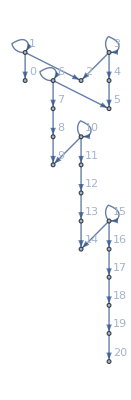

```mathematica
Graph[%112,VertexLabels->"Name"]
```